```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
y=Flatten[Import["logistic_values.csv"]];
t=N@Table[( i-1) 1000/9,{i,1, 10,1}] ;
fLogistic[t_,r_,κ_]:=2κ Exp[r t] / (κ + 2 (Exp[r t] - 1))
modelled=fLogistic[#, 0.015, 500]&/@t;
residual=y-modelled;
```

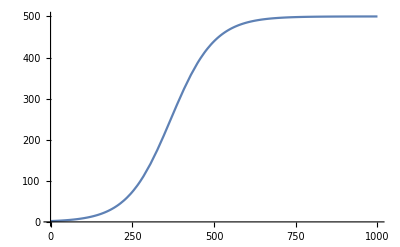

```mathematica
Plot[fLogistic[t,0.015, 500],{t,0,1000}]
```

```mathematica
LogLikelihood[NormalDistribution[0, 10],residual]
```

-37.6544

```mathematica
fGradU[r1_, κ1_, y__,t__,σ_]:=-{D[-(1/(2 σ^2))Sum[(y[[i]]-fLogistic[t[[i]],r,κ])^2,{i,1,Length@y,1}],r]/.{r->r1,κ->κ1},D[-(1/(2 σ^2))Sum[(y[[i]]-fLogistic[t[[i]],r,κ])^2,{i,1,Length@y,1}],κ]/.{r->r1,κ->κ1}}
```

```mathematica
fU[r1_,κ1_,y__,t__,σ_]:=Block[{modelled=fLogistic[#, r1, κ1]&/@t,residual},residual=y-modelled;-LogLikelihood[NormalDistribution[0, σ],residual]]
```

```mathematica
fU[0.015,500,y,t,10]
```

37.6544

```mathematica
fGradU[0.015,500,y,t,10]
```

{4888.46,-0.0683546}

```mathematica
fEulerStep[q_,p_,ϵ_,y__,t__,σ_]:=Block[{q1,p1},q1 = q + ϵ p ; p1 = p - ϵ fGradU[q1[[1]],q1[[2]],y,t,σ]; {q1,p1}]
fHMCStep[currentQ_,ϵ_,L_,width_,y__,t__,σ_]:=Block[{p = RandomVariate[NormalDistribution[0,1],2],currentP,q=currentQ,lNew,currentU,currentK,proposedU,proposedK,r,u=RandomReal[],ϵ1=width ϵ},
currentP=p; p =p - ϵ1 fGradU[q[[1]],q[[2]],y,t,σ] / 2;
lNew=Nest[fEulerStep[#[[1]],#[[2]],ϵ1,y,t,σ]&,{q,p},L-1];
p=lNew[[2]];q=lNew[[1]];q = q + ϵ1 p; p = p - ϵ1 fGradU[q[[1]],q[[2]],y,t,σ]/2; p = -p;currentU=fU[currentQ[[1]],currentQ[[2]],y,t,σ]; currentK = Sum[currentP[[i]]^2 ,{i,1,2,1}]; proposedU=fU[q[[1]],q[[2]],y,t,σ]; proposedK=Sum[p[[i]]^2 ,{i,1,2,1}]; 
r = Exp[currentU-proposedU+currentK-proposedK];If[r>u,q,currentQ]]
fHMC[numIterates_Integer,currentQ_,ϵ_,L_,width_,y__,t__,σ_]:=NestList[fHMCStep[#,ϵ,L,width,y,t,σ]&,currentQ,numIterates]
```

```mathematica
fEulerStep[{0.015,500},{1,1},0.1,y,t,10]
```

{{0.115,500.1},{20.1523,2.41805}}

```mathematica
RandomVariate[NormalDistribution[0,1],2]
```

{1.62646,-1.4374}

```mathematica
fHMC[10,{0.015,500},0.1,10,1,y,t,10]
```

$Aborted

```mathematica
fHMCStep[{0.015,500},0.1,10,{0.0001,2},y,t,10]
```

{0.0150269,502.184}

```mathematica
samples=fHMC[1000,{0.015,500},0.1,25,{0.001,1},y,t,10];
```

```mathematica
Length@DeleteDuplicates@samples
```

607

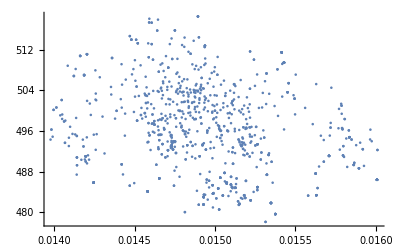

```mathematica
ListPlot[samples,PlotRange->Full]
```

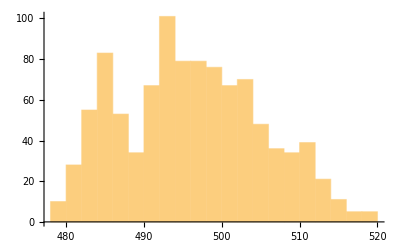

```mathematica
Histogram[samples[[All,2]]]
```